# 20 Gaussian Elimination: LU Decomposition

We know how to solve triangular systems of equations.  We are going to see how to reduce a general system 
	A.x=b 
to two triangular systems.

### Simple Matrices

What does the matrix below do?

```mathematica
L3=IdentityMatrix[8]; L3⟦4;;8,3⟧={L43,L53,L63,L73,L83};
MatrixForm[L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | 0 | 1 | 0 | 0 | 0
0 | 0 | L63 | 0 | 0 | 1 | 0 | 0
0 | 0 | L73 | 0 | 0 | 0 | 1 | 0
0 | 0 | L83 | 0 | 0 | 0 | 0 | 1)

Can you just write down its inverse?

```mathematica
MatrixForm[Inverse[L3]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | -L53 | 0 | 1 | 0 | 0 | 0
0 | 0 | -L63 | 0 | 0 | 1 | 0 | 0
0 | 0 | -L73 | 0 | 0 | 0 | 1 | 0
0 | 0 | -L83 | 0 | 0 | 0 | 0 | 1)

### Multiplying Simple Matrices

Here is another “similar” matrix

```mathematica
L4=IdentityMatrix[8]; L4⟦5;;8,4⟧={L54,L64,L74,L84};
MatrixForm[L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | L54 | 1 | 0 | 0 | 0
0 | 0 | 0 | L64 | 0 | 1 | 0 | 0
0 | 0 | 0 | L74 | 0 | 0 | 1 | 0
0 | 0 | 0 | L84 | 0 | 0 | 0 | 1)

The product L3.L4 is simple

```mathematica
MatrixForm[L3.L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83 | L84 | 0 | 0 | 0 | 1)

However, the product L4.L3 is not. To use these matrices we need to wrok down.

```mathematica
MatrixForm[L4.L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53+L43 L54 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63+L43 L64 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73+L43 L74 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83+L43 L84 | L84 | 0 | 0 | 0 | 1)

### Chaining Simple Matrices

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

The lower triangular matrix below is the product of 7 of these simple matrices.

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
L21 | 1 | 0 | 0 | 0 | 0 | 0 | 0
L31 | L32 | 1 | 0 | 0 | 0 | 0 | 0
L41 | L42 | L43 | 1 | 0 | 0 | 0 | 0
L51 | L52 | L53 | L54 | 1 | 0 | 0 | 0
L61 | L62 | L63 | L64 | L65 | 1 | 0 | 0
L71 | L72 | L73 | L74 | L75 | L76 | 1 | 0
L81 | L82 | L83 | L84 | L85 | L86 | L87 | 1)

## Using these Simple Matrices to Create Zeros

### Manually

Gaussian Elimination is the first way people worked out to make zeros. Note, if you were solving equations by candle light in 18XX you would not organize it this way!

```mathematica
m=8;
A0=RandomReal[{-1,1},{m,m}];
L1=IdentityMatrix[m]; L1⟦2;;m,1⟧=A0⟦2;;m,1⟧/A0⟦1,1⟧;
MatrixForm[A1 = Inverse[L1].A0]
```

(-0.817983 | 0.214012 | -0.619233 | 0.660302 | -0.489296 | -0.366809 | -0.777392 | 0.816557
-5.67729×10^-17 | 0.604687 | 0.0631193 | 1.05984 | -1.08896 | 0.362484 | 0.0302655 | 0.171948
-1.25714×10^-17 | 0.362428 | 0.56412 | 0.207099 | 0.717936 | 0.481121 | -0.166787 | 0.344144
-4.59424×10^-17 | 0.44712 | -0.542352 | 0.607843 | -1.39214 | -0.53845 | -0.705515 | 1.71887
3.03228×10^-17 | 0.175969 | -0.784727 | 1.4642 | -0.716125 | 0.355317 | -0.753925 | 1.83696
-1.11022×10^-16 | 0.000662715 | 1.29239 | -0.660322 | 0.150369 | -0.366809 | 0.525086 | -0.629896
0. | -0.611775 | 0.264525 | -0.983191 | 0.94928 | -0.197653 | -0.742376 | -1.17206
0. | 0.194714 | 1.10979 | -1.08195 | 0.141367 | 0.0552784 | -0.0763834 | -0.67615)

If we do it again we can make another almost column of zeros.

```mathematica
L2=IdentityMatrix[m]; L2⟦3;;m,2⟧=A1⟦3;;m,2⟧/A1⟦2,2⟧;
MatrixForm[A2 = Chop[Inverse[L2].A1]]
```

(-0.817983 | 0.214012 | -0.619233 | 0.660302 | -0.489296 | -0.366809 | -0.777392 | 0.816557
0 | 0.604687 | 0.0631193 | 1.05984 | -1.08896 | 0.362484 | 0.0302655 | 0.171948
0 | 0 | 0.526289 | -0.428134 | 1.37062 | 0.263861 | -0.184927 | 0.241084
0 | 0 | -0.589024 | -0.17583 | -0.58694 | -0.80648 | -0.727894 | 1.59173
0 | 0 | -0.803095 | 1.15578 | -0.399228 | 0.249831 | -0.762732 | 1.78692
0 | 0 | 1.29232 | -0.661484 | 0.151562 | -0.367206 | 0.525053 | -0.630085
0 | 0 | 0.328384 | 0.0890749 | -0.152444 | 0.169081 | -0.711756 | -0.998097
0 | 0 | 1.08947 | -1.42322 | 0.49202 | -0.0614443 | -0.0861291 | -0.731519)

We can keep going.

```mathematica
L3=IdentityMatrix[m]; L3⟦4;;m,3⟧=A2⟦4;;m,3⟧/A2⟦3,3⟧;
MatrixForm[A3 = Chop[Inverse[L3].A2]]
L4=IdentityMatrix[m]; L4⟦5;;m,4⟧=A3⟦5;;m,4⟧/A3⟦4,4⟧;
MatrixForm[A4 = Chop[Inverse[L4].A3]]
L5=IdentityMatrix[m]; L5⟦6;;m,5⟧=A4⟦6;;m,5⟧/A4⟦5,5⟧;
MatrixForm[A5 = Chop[Inverse[L5].A4]]
L6=IdentityMatrix[m]; L6⟦7;;m,6⟧=A5⟦7;;m,6⟧/A5⟦6,6⟧;
MatrixForm[A6 = Chop[Inverse[L6].A5]]
L7=IdentityMatrix[m]; L7⟦8;;m,7⟧=A6⟦8;;m,7⟧/A6⟦7,7⟧;
MatrixForm[A7 = Chop[Inverse[L7].A6]]
```

(-0.817983 | 0.214012 | -0.619233 | 0.660302 | -0.489296 | -0.366809 | -0.777392 | 0.816557
0 | 0.604687 | 0.0631193 | 1.05984 | -1.08896 | 0.362484 | 0.0302655 | 0.171948
0 | 0 | 0.526289 | -0.428134 | 1.37062 | 0.263861 | -0.184927 | 0.241084
0 | 0 | 0 | -0.654997 | 0.947062 | -0.511166 | -0.934864 | 1.86155
0 | 0 | 0 | 0.502462 | 1.69228 | 0.652472 | -1.04492 | 2.1548
0 | 0 | 0 | 0.389811 | -3.21404 | -1.01512 | 0.979147 | -1.22207
0 | 0 | 0 | 0.356214 | -1.00766 | 0.00444163 | -0.596369 | -1.14852
0 | 0 | 0 | -0.536946 | -2.34529 | -0.60766 | 0.296687 | -1.23058)

(-0.817983 | 0.214012 | -0.619233 | 0.660302 | -0.489296 | -0.366809 | -0.777392 | 0.816557
0 | 0.604687 | 0.0631193 | 1.05984 | -1.08896 | 0.362484 | 0.0302655 | 0.171948
0 | 0 | 0.526289 | -0.428134 | 1.37062 | 0.263861 | -0.184927 | 0.241084
0 | 0 | 0 | -0.654997 | 0.947062 | -0.511166 | -0.934864 | 1.86155
0 | 0 | 0 | 0 | 2.41879 | 0.260346 | -1.76208 | 3.58283
0 | 0 | 0 | 0 | -2.65041 | -1.31934 | 0.422777 | -0.114203
0 | 0 | 0 | 0 | -0.492609 | -0.273551 | -1.10479 | -0.136139
0 | 0 | 0 | 0 | -3.12166 | -0.188623 | 1.06306 | -2.75662)

(-0.817983 | 0.214012 | -0.619233 | 0.660302 | -0.489296 | -0.366809 | -0.777392 | 0.816557
0 | 0.604687 | 0.0631193 | 1.05984 | -1.08896 | 0.362484 | 0.0302655 | 0.171948
0 | 0 | 0.526289 | -0.428134 | 1.37062 | 0.263861 | -0.184927 | 0.241084
0 | 0 | 0 | -0.654997 | 0.947062 | -0.511166 | -0.934864 | 1.86155
0 | 0 | 0 | 0 | 2.41879 | 0.260346 | -1.76208 | 3.58283
0 | 0 | 0 | 0 | 0 | -1.03406 | -1.50803 | 3.81171
0 | 0 | 0 | 0 | 0 | -0.220529 | -1.46365 | 0.593538
0 | 0 | 0 | 0 | 0 | 0.147377 | -1.21106 | 1.86734)

(-0.817983 | 0.214012 | -0.619233 | 0.660302 | -0.489296 | -0.366809 | -0.777392 | 0.816557
0 | 0.604687 | 0.0631193 | 1.05984 | -1.08896 | 0.362484 | 0.0302655 | 0.171948
0 | 0 | 0.526289 | -0.428134 | 1.37062 | 0.263861 | -0.184927 | 0.241084
0 | 0 | 0 | -0.654997 | 0.947062 | -0.511166 | -0.934864 | 1.86155
0 | 0 | 0 | 0 | 2.41879 | 0.260346 | -1.76208 | 3.58283
0 | 0 | 0 | 0 | 0 | -1.03406 | -1.50803 | 3.81171
0 | 0 | 0 | 0 | 0 | 0 | -1.14204 | -0.219369
0 | 0 | 0 | 0 | 0 | 0 | -1.42598 | 2.41059)

(-0.817983 | 0.214012 | -0.619233 | 0.660302 | -0.489296 | -0.366809 | -0.777392 | 0.816557
0 | 0.604687 | 0.0631193 | 1.05984 | -1.08896 | 0.362484 | 0.0302655 | 0.171948
0 | 0 | 0.526289 | -0.428134 | 1.37062 | 0.263861 | -0.184927 | 0.241084
0 | 0 | 0 | -0.654997 | 0.947062 | -0.511166 | -0.934864 | 1.86155
0 | 0 | 0 | 0 | 2.41879 | 0.260346 | -1.76208 | 3.58283
0 | 0 | 0 | 0 | 0 | -1.03406 | -1.50803 | 3.81171
0 | 0 | 0 | 0 | 0 | 0 | -1.14204 | -0.219369
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.6845)

### Script

All this typing is nuts.  All the L entries can be stored in the same place.  We can recycle the storage for the matrix that winds up being U (the things called A0, A1, …) up above.  Finally, since only a few rows of the matrix are changed at a time changed at a time we might as well do only those rows

1.60848×10^-15

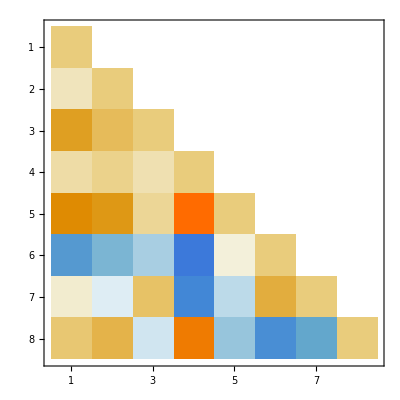
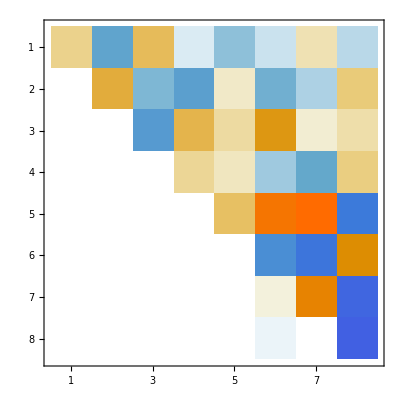

```mathematica
m=8;
A=RandomReal[{-1,1},{m,m}];
(* Start Script *)
L=IdentityMatrix[m];
U=A; 
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}]
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

### Function

## Solving a Linear System with an LU Decomposition

We know how to solve triangular systems. we even know that the obvious algorithm is backwards stable. We now know how to split a matrix up into two triangular matrices A=L.U.  we should be able to put this together to get an algorithm to solve A.x=L.U.x=b. All we need to do is make up an intermediate variable.  y=U.x 
	L.(U.x)=L.y=b
Solve L.y=b to get a ỹ.  Then solve U.x=ỹ to get x̃.  Since the triangular solves are backwards stable this would all be great if the L.U decomposition was stable!  It is not!

### Need for Pivoting

There are perfectly well behaved linear systems which will break our first attempt at an LU decomposition.  For example
	(ϵ | 1.0
1.0 | 1.0).(x1
x2)=(b1
b2).
In exact arithmetic Gaussian elimination gives the solution
	x1 | = | (b1-b2)/(-1+ϵ) | ⟶ | b2-b1
x2 | = | (-b1+b2 ϵ)/(-1+ϵ) | ⟶ | b1
The system is fine as ϵ→0.  Our first attempt at an LU decomposition gives. 
	A=(ϵ | 1.0
1.0 | 1.0)=(1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | 1-ϵ^-1)
which in exact arithmetic works just fine: exact arithmetic does not care that ϵ^-1 could be huge. On any computer this is a real problem!  When ϵ is small in floating point the last entry gets messed up and we will get 
	 (1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | -ϵ^-1)=(ϵ | 1
1 | 0)

The sad thing is this has nothing to do with the equations/matrix. As ϵ→0 the condition number κ(A) is the singular value ratio of ratio of (0 | 1.0
1.0 | 1.0) which is roughly 3.

The really sad thing is that if we had just written down the equations in a different order we would have got (1.0 | 1.0
ϵ | 1.0)=(1 | 0
ϵ | 1)(1 | 1
0 | 1-ϵ) which would have worked just fine.

We can not write a usage guide for a function that says “make sure your equations” are in a decent order. We need to make an algorithm that reorders the equations (rows in the matrix) into a good order on the fly.

The first question is given a matrix A which row (same as equation) should we start with.

After the first row we just ask which of the remaining rows is best to do next.

The resulting algorithm is called an LU decomposition with row pivoting.

You can also ask which remaining variable (column of the matrix would be best) which gives column pivoting.

If you ask which is the best variable and equation you are doing complete pivoting!